```mathematica
NN = 100

m0[a_] := ⅇ^(1/NN Log[a])

σ0[a_] := ⅇ^(1/NN Log[ 1 + a])



mj[a_,j_] := m0[a] ⅇ^(2 π ⅈ j / NN)

m1[a_] := m0[a] ⅇ^(2 π ⅈ  / NN)

σ1[a_] := σ0[a]  ⅇ^((2 π ⅈ)/NN)



W0[a_] := (- 1)/(2π)( NN σ0[a] + ∑_(j=0)^(NN-1) mj[a,j] Log[ σ0[a] - mj[a,j] ])



W1[a_] := -1/(2π) (NN σ1[a] + ∑_(j=0)^(NN-1) mj[a,j] Log[ σ1[a] - mj[a,j] ] )



Tower[a_, k_] := (( ⅇ^(2 π ⅈ / NN) - 1 ) W0[a] + ⅈ mj[a,k])/(m1[a] - m0[a])
```

100

```mathematica
rmax = ⅇ^2
logz[x_,y_] := ⅇ^(ⅈ Arg[ x + ⅈ y]) (x^2 + y^2)^(NN/2)
```

ⅇ^2

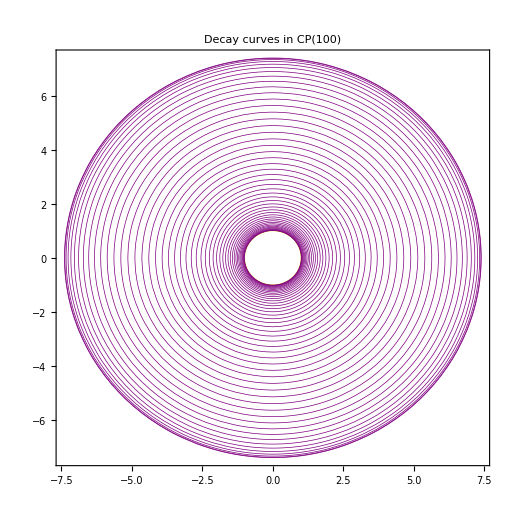

```mathematica
ContourPlot[    Evaluate[  Table[ x^2 + y^2 == ( ⅇ^(1 - Cos[2 π k / NN]))^2, { k, Ceiling[NN/2]} ] ], 
                             { x , -rmax, rmax}, { y, -rmax, rmax },
                             ContourStyle->
                          Join[ { Directive[ Thickness[0.001], Yellow ]  },
                       Table[ Directive[ Thickness[0.001], Purple ], {k,NN-1}] ] ,
                            PlotLabel-> Style["Decay curves in CP(100)",FontSize->24], LabelStyle->Directive[FontSize->18] ]
```